```mathematica
f1[i_]:=DialogInput[DynamicModule[{p={0,0},q = 0},
{Column[{StringJoin[{"Charge ",ToString[i]}],Row[{Column[{Slider2D[Dynamic[p],{{-5,-5},{5,5},{0.5,0.5}}],
Dynamic[p]}],
Column[{TextCell["Charge Value of Charged Particle in Coloumbs"],
InputField[Dynamic[q],Number],
DefaultButton["OK",DialogReturn[{p,q}]]}]}]}]}]];
```

```mathematica
f2[i_]:=DialogInput[DynamicModule[{n},Column[{"Number of Charged Particles Contributing to Electric Field",InputField[Dynamic[n],Number],DefaultButton["OK",DialogReturn[n]]}]]];
```

```mathematica
g[i_]:=componentNames[[i]]∈"EFieldLine.Components.CParticle";
h[i_]:=componentNames[[i]]<>".field"-> "tparticle1.E";
```

```mathematica
j[i_]:=componentNames[[i]]<>".q"-> chargeInfo[[i]][[2]];
k[i_]:=componentNames[[i]]<>".x"-> chargeInfo[[i]][[1]][[1]];
m[i_]:=componentNames[[i]]<>".y"-> chargeInfo[[i]][[1]][[2]];
```

```mathematica
nCharges=f2[1]
```

4

```mathematica
chargeInfo = Table[f1[i],{i,1,nCharges}]
```

{{{-5,-5},1},{{5.,-5},1},{{0.,5.},2},{{0,0},-1}}

```mathematica
componentNames=Table["c"<>ToString[i],{i,1,nCharges}]
```

{c1,c2,c3,c4}

```mathematica
components=Append[Table[g[x],{x,1,nCharges}],"tparticle1" ∈"EFieldLine.Components.TParticle"]
connections=Table[h[x],{x,1,nCharges}]
```

{c1∈EFieldLine.Components.CParticle,c2∈EFieldLine.Components.CParticle,c3∈EFieldLine.Components.CParticle,c4∈EFieldLine.Components.CParticle,tparticle1∈EFieldLine.Components.TParticle}

{c1.field→tparticle1.E,c2.field→tparticle1.E,c3.field→tparticle1.E,c4.field→tparticle1.E}

```mathematica
Needs["WSMLink`"]
```

```mathematica
Append[components,"tparticle1" ∈"EFieldLine.Components.TParticle"]
```

{c1∈EFieldLine.Components.CParticle,c2∈EFieldLine.Components.CParticle,c3∈EFieldLine.Components.CParticle,c4∈EFieldLine.Components.CParticle,tparticle1∈EFieldLine.Components.TParticle}

```mathematica
components
```

{c1∈EFieldLine.Components.CParticle,c2∈EFieldLine.Components.CParticle,c3∈EFieldLine.Components.CParticle,c4∈EFieldLine.Components.CParticle,tparticle1∈EFieldLine.Components.TParticle}

```mathematica
model=WSMConnectComponents["Attempt",components,connections]
```

-Graphics-

```mathematica
WSMSetValues[model,Table[j[x],{x,1,nCharges}]]
WSMSetValues[model,Table[k[x],{x,1,nCharges}]]
WSMSetValues[model,Table[m[x],{x,1,nCharges}]]
```

{c1.q→1,c2.q→1,c3.q→2,c4.q→-1}

{c1.x→-5,c2.x→5.,c3.x→0.,c4.x→0}

{c1.y→-5,c2.y→-5,c3.y→5.,c4.y→0}

```mathematica
createStartPoints[x0_,y0_,r_,n_]:=Table[{r*Cos[theta]+x0,r*Sin[theta]+y0},{theta,0,2*Pi,2*Pi/n}];
singleEfieldLineSim[{x0_, y0_}]:= WSMSimulate["Attempt", {0,100},WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}];
multipleEfieldLineSims[x0_,y0_,r_,n_]:=Map[singleEfieldLineSim,createStartPoints[x0,y0,r,n]];
```

```mathematica
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
```

```mathematica
For[i=1,i≤nCharges,i++,mR1 = multipleEfieldLineSims[chargeInfo[[i]][[1]][[1]],chargeInfo[[i]][[1]][[2]],0.25,20];
yR1=Table[mR1[[x]]["tparticle1.y"],{x,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[y]]["tparticle1.x"],{y,1,Dimensions[mR1][[1]]}];
results[[i]]=Table[EpPlot[z],{z,1,Dimensions[mR1][[1]]}]]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 42.5426"

WSMSimulate::term: Simulation of "Attempt" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "Attempt" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

```mathematica
Cancel
```

Cancel

```mathematica
Cancel::usage
```

Cancel[expr] cancels out common factors in the numerator and denominator of expr.

```mathematica
CancelButton
```

CancelButton

```mathematica
Information[CancelButton]
```

CancelButton[] represents a Cancel button in a dialog that closes the dialog window when clicked.
CancelButton[action] represents a button labeled Cancel that evaluates action when clicked.
CancelButton[label,action] uses label as the label for the button.

Attributes[CancelButton]={HoldAll,Protected,ReadProtected}
 
Options[CancelButton]={Active→True,Alignment→Automatic,Appearance→CancelButton,AutoAction→False,Background→Automatic,BaselinePosition→Automatic,BaseStyle→GenericButton,ContentPadding→True,DefaultBaseStyle→Button,Enabled→Automatic,Evaluator→Automatic,FrameMargins→Automatic,ImageMargins→0,ImageSize→Full,Method→Preemptive}

```mathematica
i
```

1

```mathematica
results
```

results

```mathematica
Information[results]
```

Global`results

```mathematica
results[[1]]
```

Part::partd: Part specification results ⟦ 1 ⟧ is longer than depth of object.

results⟦1⟧

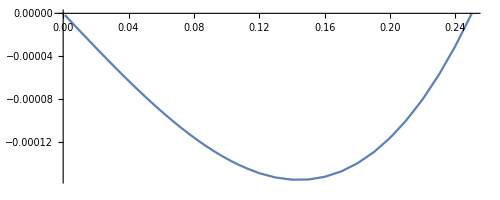
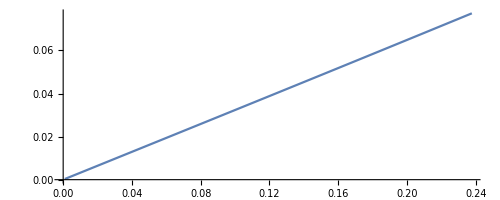
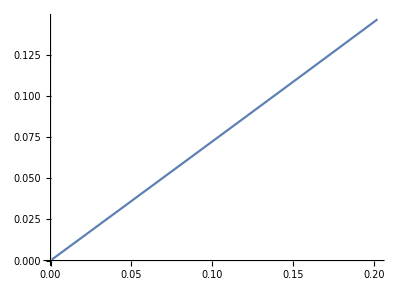
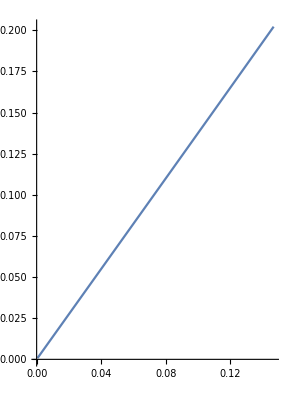
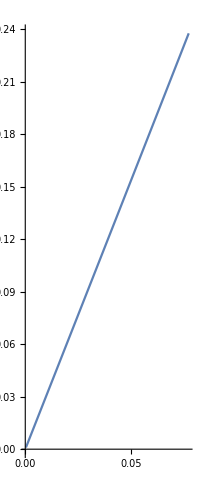
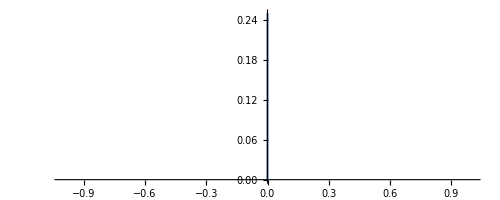
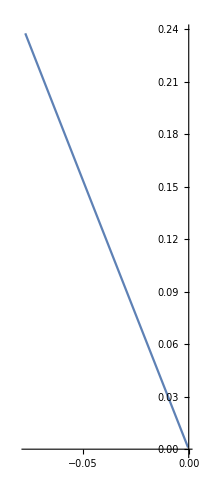
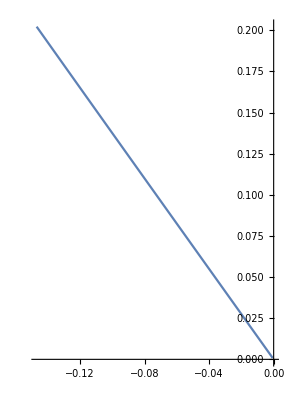
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
results
```

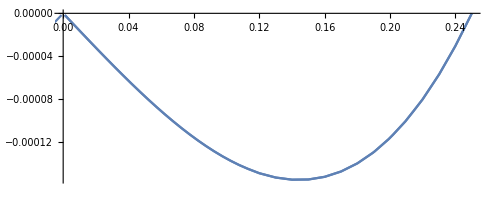

```mathematica
Show[results]
```

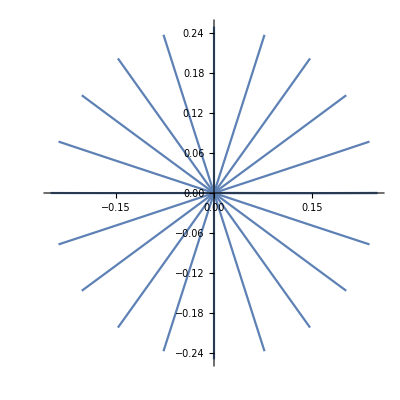

```mathematica
Show[results,PlotRange->All]
```

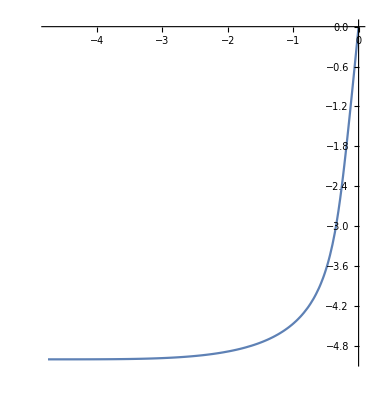
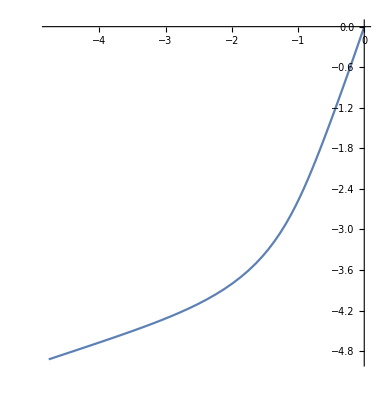
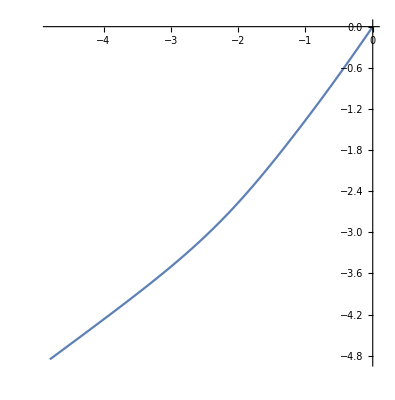
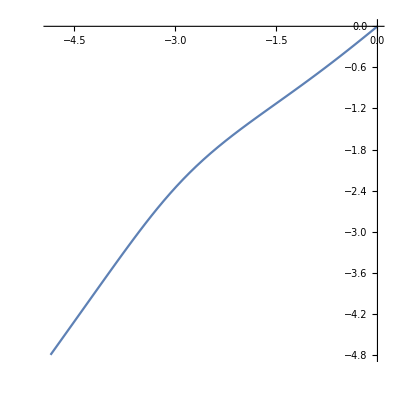
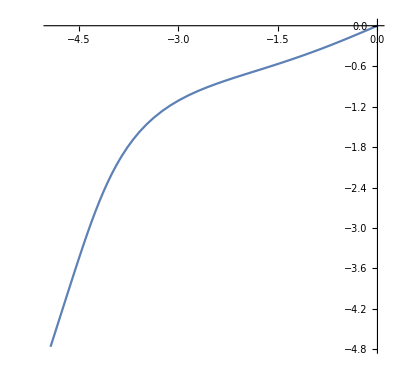
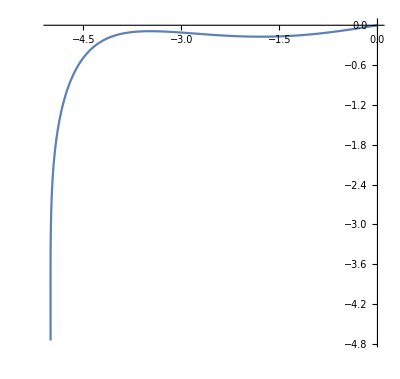
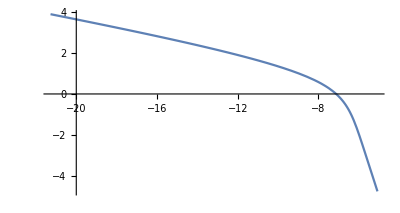
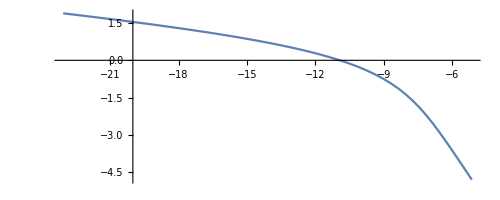
{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
results
```

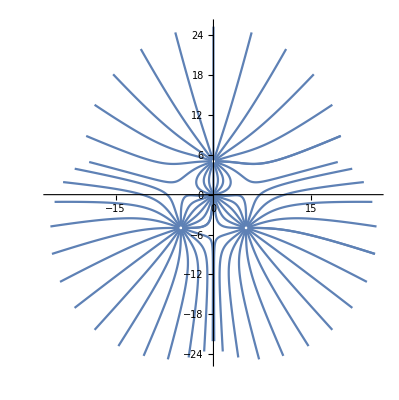

```mathematica
Show[results,PlotRange->All]
```

```mathematica
Show[%82,ImageSize->Full]
```

-Graphics-